```mathematica
teoricos = Import["teorico.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
Importar[fileName_] := Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"qpu-results", fileName}], "Dataset", "HeaderLines"->1]
```

```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`
```

```mathematica
backends = {"ibm_brisbane", "ibm_sherbrooke"};(*, "ibm_kyiv"*)
```

```mathematica
latexStyle = {FontFamily ->  "LM Roman 12"};
```

```mathematica
ps = {0, 0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8, 0.9, 1};puntosParaDataset[ds_] := Table[{p, ds[Select[(#chA == "ADC" && #chB == "ADC" && #d =="fidelity" && #pA ==p && #pB ==p)&], "score"][1]}, {p, ps}];
puntosParaDatasetFNWN[ds_] := Table[{p, ds[Select[(#chA == "ADC" && #chB == "ADC" && #d =="fidelity" && #pA ==0.85 && #pB ==p)&], "score"][1]}, {p, ps}];
```

```mathematica
experimentosDiagonal={"diagonal_unoptimized", "diagonal_QPU_optimized", "diagonal_QPU_optimized_EM"};
```

```mathematica
GraficarParaBackend[backend_] := ListPlot[{puntosParaDataset[teoricos]}~Join~Table[puntosParaDataset[Importar[backend<>"_"<>exp<>".csv"]], {exp, experimentosDiagonal}], PlotLegends->(Text[#, BaseStyle->latexStyle]&)/@({"teóricos"}~Join~experimentosDiagonal), BaseStyle -> latexStyle];
```

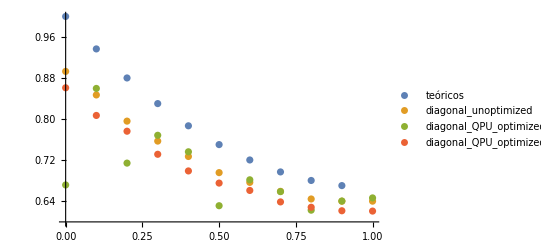

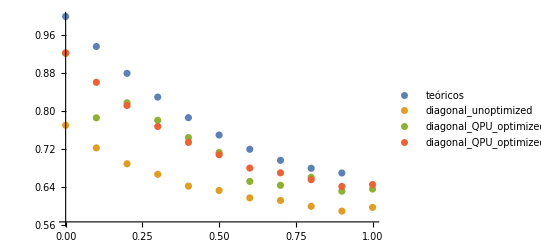

```mathematica
Do[Print[GraficarParaBackend[backend]], {backend, backends}]
```

```mathematica
Show[ListPlot[puntosParaDataset[teoricos]],line]
```

-Graphics-

```mathematica
plot = ListPlot[Table[Labeled[puntosParaDatasetFNWN[Importar[backend<>"_fighting_noise_with_noise.csv"]], backend], {backend, backends}], BaseStyle -> latexStyle];
line=Plot[Labeled[0.6666, MaTeX["\langle \\bar{F} \\rangle_{cl}"]],{x,0,1}];Show[plot,line, PlotRange->Automatic, BaseStyle -> latexStyle]
```

-Graphics-